## Setup

```mathematica
outputDir1p3="/media/bazow/Data1/output_check_theta/output_022916_t1p3";
```

```mathematica
outputDir1p8="/media/bazow/Data1/output_check_theta/output_030116_t1p8";
```

```mathematica
hbarc=0.197326938;
```

```mathematica
Nc=3;
Nf=2.5;
fac=3(2(Nc^2-1)+7/2Nc*Nf)Pi^2/90;
facT=fac^(1/4);
```

```mathematica
tstr[t_]:=Module[{len,n,pad},
len=Length[StringSplit[ToString[t],"."]];
If[len==1,
n=0,
n=StringLength[StringSplit[ToString[t],"."][[2]]];
];
pad="";
If[n==0,
pad=".000";,
If[n==1,
pad="00";,
If[n==2,
pad="0";
]]];
Return[ToString[t]<>pad]
]
```

### Caption Functions

```mathematica
myLegendItem[color_,fillopacity_,dashing_,thickness_,text_,voffset_,textoffset_]:={color,Opacity[fillopacity],Rectangle[{0,voffset-0.05},{0.5,voffset+0.05}],Opacity[1.0],dashing,AbsoluteThickness[thickness],Line[{{0,voffset},{0.5,voffset}}],Black,Text[text,{0.72+textoffset,voffset}]}
```

```mathematica
myLegendItemTriangles[color_,text_,voffset_,textoffset_]:={color,EdgeForm[{AbsoluteThickness[1]}],Polygon[{{0,voffset-0.025},{0.05,voffset-0.025},{0.025,0.025*Sqrt[3]+voffset-0.025}}],Polygon[{{0+0.1,voffset-0.025},{0.05+0.1,voffset-0.025},{0.025+0.1,0.025*Sqrt[3]+voffset-0.025}}],Polygon[{{0+0.2,voffset-0.025},{0.05+0.2,voffset-0.025},{0.025+0.2,0.025*Sqrt[3]+voffset-0.025}}],Polygon[{{0+0.3,voffset-0.025},{0.05+0.3,voffset-0.025},{0.025+0.3,0.025*Sqrt[3]+voffset-0.025}}],Polygon[{{0+0.4,voffset-0.025},{0.05+0.4,voffset-0.025},{0.025+0.4,0.025*Sqrt[3]+voffset-0.025}}],EdgeForm[],Black,Text[text,{0.85+textoffset,voffset}]}
```

```mathematica
myLegendItemSquares[color_,text_,voffset_,textoffset_]:={color,EdgeForm[{AbsoluteThickness[1]}],Rectangle[{0.0+0.0,voffset-0.025},{0.05+0.0,voffset+0.025}],Rectangle[{0.0+0.1,voffset-0.025},{0.05+0.1,voffset+0.025}],Rectangle[{0.0+0.2,voffset-0.025},{0.05+0.2,voffset+0.025}],Rectangle[{0.0+0.3,voffset-0.025},{0.05+0.3,voffset+0.025}],Rectangle[{0.0+0.4,voffset-0.025},{0.05+0.4,voffset+0.025}],Black,Text[text,{0.85+textoffset,voffset}]}
```

```mathematica
myLegendItemPoints[color_,text_,voffset_,textoffset_]:={color,EdgeForm[{AbsoluteThickness[1],Black}],Disk[{0.025,voffset},0.025],Disk[{0.025+0.1,voffset},0.025],Disk[{0.025+0.2,voffset},0.025],Disk[{0.025+0.3,voffset},0.025],Disk[{0.025+0.4,voffset},0.025],EdgeForm[],Black,Text[text,{0.85+textoffset,voffset}]}
```

```mathematica
myLegendItemNoLine[color_,fillopacity_,text_,voffset_,textoffset_]:={color,Opacity[fillopacity],EdgeForm[{Opacity[0.5],AbsoluteThickness[1],Brown}],Rectangle[{0,voffset-0.05},{0.5,voffset+0.05}],Opacity[1.0],RGBColor[0.8,0.8,0.9],AbsoluteThickness[0],Line[{{0.1,voffset},{0.1,voffset}}],Black,Text[text,{0.85+textoffset,voffset}]}
```

### Legends

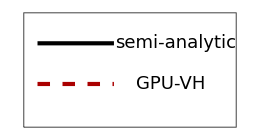

```mathematica
legend=Graphics[{White,EdgeForm[Directive[Thin,Lighter[Black]]],Rectangle[{-.09,.15},{1.3,0.6}],EdgeForm[],Opacity[1],myLegendItem[Black,0,Null,3,Style["semi-analytic",18],0.48,0.18],myLegendItem[Darker[Red],0,Dashing[Medium],3,Style["GPU-VH",18],0.32,0.15]},ImageSize->{260,140}]
```

## Compare conformal viscous fluid dynamics Bjorken

```mathematica
outputDir="/media/bazow/Data1/output_gpu/256-256-32";
```

```mathematica
eint[t_?NumericQ]:=Interpolation[Import[outputDir<>"/e_"<>ToString[PaddedForm[t,{3,3},NumberPadding->{"", "0"}]]<>".dat"],InterpolationOrder->3][0,0,0]
edataT=Table[{t,eint[t]},{t,1,3.5,.05}];
eIntT=Interpolation[edataT,InterpolationOrder->3]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3,3,1}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

InterpolatingFunction[{{1., 3.5}}, <>]

```mathematica
Plot[(eIntT[t]/fac)^(1/4)*.197,{t,1,1.2}]
```

### 2nd order viscous hydro

```mathematica
Clear[t,t0,tf,etabar,T0,beta,pi0,teqVH,gamma2,eiso,piso]
```

```mathematica
t0=1;
tf=20;
```

```mathematica
etabar=0.2;
```

```mathematica
T0=3.05;
```

```mathematica
beta=38/21;
```

```mathematica
pi0=0;
```

```mathematica
teqVH[T_]=5*etabar/T;
```

```mathematica
gamma2=(30/(37 Pi^2))^(1/4);(*equation of state*)
gamma2=1;
eiso[p_]=(p/gamma2)^4;
piso[p_]=eiso[p]/3;
```

```mathematica
solVH=NDSolve[{D[eiso[T[t]],t]==-(eiso[T[t]]+piso[T[t]])/t+pi[t]/t,D[pi[t],t]==-pi[t]/teqVH[T[t]]+16piso[T[t]]/15/t-beta*pi[t]/t,T[t0]==T0,pi[t0]==pi0},{T,pi},{t,t0,tf}];
```

```mathematica
TSolVH=T/.solVH[[1]];
piSolVH=pi/.solVH[[1]];
```

```mathematica
eVH[t_]=eiso[TSolVH[t]]/eiso[TSolVH[t0]];
plVH[t_]=3(piso[TSolVH[t]]-piSolVH[t])/eiso[TSolVH[t0]];
ptVH[t_]=3(piso[TSolVH[t]]+piSolVH[t]/2)/eiso[TSolVH[t0]];
plVH[t_]=(piso[TSolVH[t]]-piSolVH[t])/piso[TSolVH[t0]];
ptVH[t_]=(piso[TSolVH[t]]+piSolVH[t]/2)/piso[TSolVH[t0]];
```

### plot

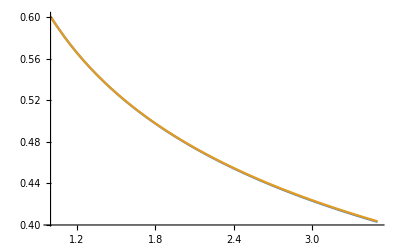

```mathematica
Plot[{eiso[TSolVH[t]]^(1/4)*.197,(eIntT[t]/fac)^(1/4)*.197},{t,1,3.5}]
```

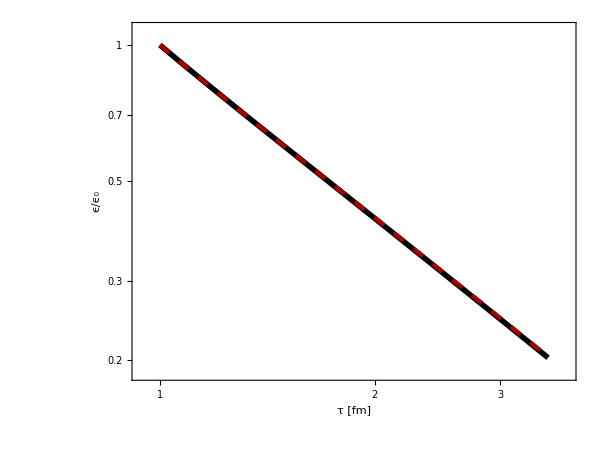

```mathematica
ePlotBjorken=LogLogPlot[{eVH[t],eIntT[t]/eIntT[1]},{t,1,3.5},PlotRange->All,PlotStyle->{{AbsoluteThickness[4],Darker[Black]},{AbsoluteThickness[3],Dashing[Medium],Darker[Red]}},Frame->True,Axes->False,FrameLabel->{"τ [fm]","ϵ/ϵ_0"},FrameStyle->Directive[AbsoluteThickness[1.1]],BaseStyle->{FontFamily->"Times",FontSize->20},ImageSize->600,AspectRatio->0.75,ImagePadding->{{85,30},{80,20}},Epilog->{Inset[legend,{2.75,.9}]}]
```

```mathematica
Export["/home/bazow/git/gpu-vh/mathematica/bjorkenFlowTestPlot.pdf",ePlotBjorken]
```

/home/bazow/git/gpu-vh/mathematica/bjorkenFlowTestPlot.pdf

## Compare 3+1d code to Ideal Gubser

```mathematica
ux[t_,x_,y_,{q_}]:=x*Sinh[ArcTanh[2q t q Sqrt[x^2+y^2]/(1+q^2t^2+q^2(x^2+y^2))]]/Sqrt[x^2+y^2]
```

```mathematica
temp[t_,r_,{T0_,q_}]:=T0(2q*t)^(2/3)/(t(1+2q^2(t^2+r^2)+q^4(t^2-r^2)^2)^(1/3))
```

```mathematica
temp2[t_,x_,y_,{T0_,q_}]:=T0(2q*t)^(2/3)/(t(1+2q^2(t^2+x^2+y^2)+q^4(t^2-x^2-y^2)^2)^(1/3))
```

```mathematica
outputDir="/media/bazow/Data1/output_gpu/256-256-32";
```

```mathematica
.77+.84
```

1.61

```mathematica
.6/.197
```

3.04569

```mathematica
t=3.5;
lim=4.9;
dataEd=Import[outputDir<>"/e_"<>tstr[t]<>".dat"];
eInt=Interpolation[dataEd,InterpolationOrder->3];
dataux=Import[outputDir<>"/ux_"<>tstr[t]<>".dat"];
uxInt=Interpolation[dataux,InterpolationOrder->3];
ePlotIdeal=Plot[{fac*temp2[t,x,0,{1.2,1}]^4,eInt[x,0,0]},{x,-lim,lim},PlotRange->All,PlotStyle->{{AbsoluteThickness[4],Darker[Black]},{AbsoluteThickness[3],Dashing[Medium],Darker[Red]}},Frame->True,Axes->False,FrameLabel->{"x [fm]","ϵ[fm^-4]"},FrameStyle->Directive[AbsoluteThickness[1.1]],BaseStyle->{FontFamily->"Times",FontSize->20},ImageSize->600,AspectRatio->0.75,ImagePadding->{{85,30},{80,20}}];
uxPlotIdeal=Plot[{ux[t,x,0,{1}],uxInt[x,0,0]},{x,-lim,lim},PlotRange->All,PlotStyle->{{AbsoluteThickness[4],Darker[Black]},{AbsoluteThickness[3],Dashing[Medium],Darker[Red]}},Frame->True,Axes->False,FrameLabel->{"x [fm]","u^x"},FrameStyle->Directive[AbsoluteThickness[1.1]],BaseStyle->{FontFamily->"Times",FontSize->20},ImageSize->600,AspectRatio->0.75,Epilog->{Inset[legend,{2,-2.5}],Inset["τ_0="<>ToString[1]<>"fm, τ_f="<>ToString[t]<>" fm, 4πη/𝒮 = "<>ToString[fpieb],{-1,3}]},ImagePadding->{{85,30},{80,20}}];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3,3,1}.

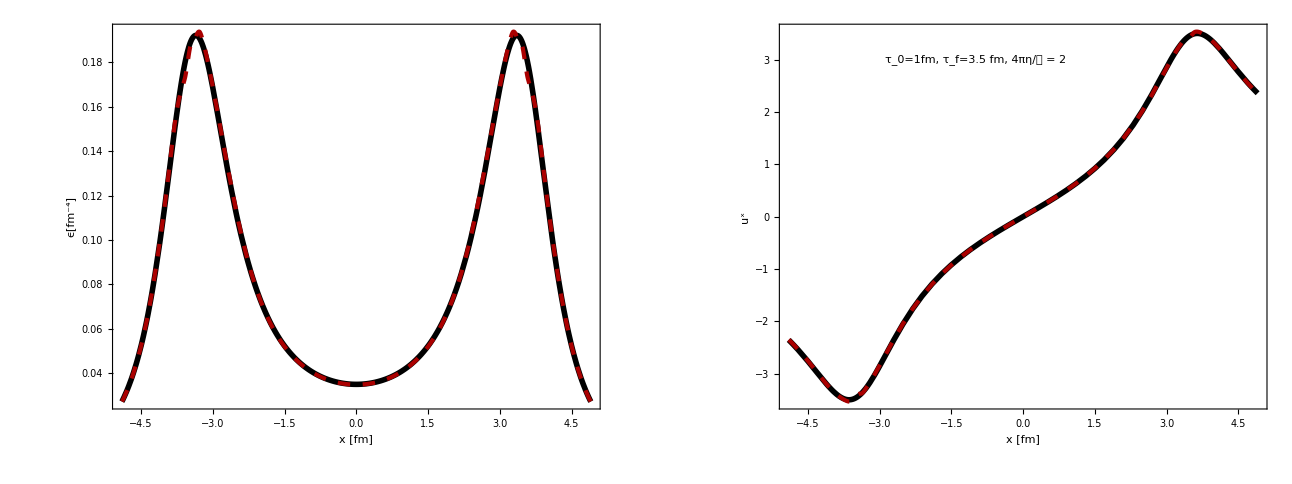

```mathematica
pltIdeal=GraphicsGrid[{{ePlotIdeal,uxPlotIdeal}}]
```

```mathematica
Export["/home/bazow/git/gpu-vh/mathematica/gubserIdealFlowTestPlot.pdf",pltIdeal]
```

/home/bazow/git/gpu-vh/mathematica/gubserIdealFlowTestPlot.pdf

Interpolation::inhr: Requested order is too high; order has been reduced to {3,3,1}.

InterpolatingFunction[{{-4.975, 4.975}, {-4.975, 4.975}, {-0.025, 0.025}}, <>]

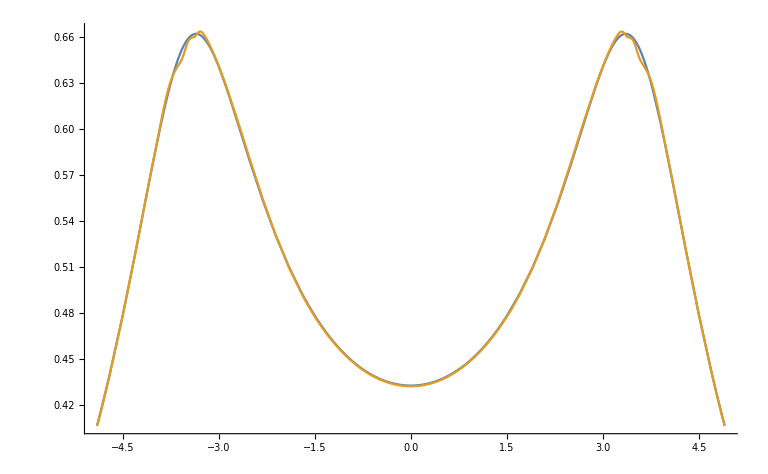

Interpolation::inhr: Requested order is too high; order has been reduced to {3,3,1}.

InterpolatingFunction[{{-4.975, 4.975}, {-4.975, 4.975}, {-0.025, 0.025}}, <>]

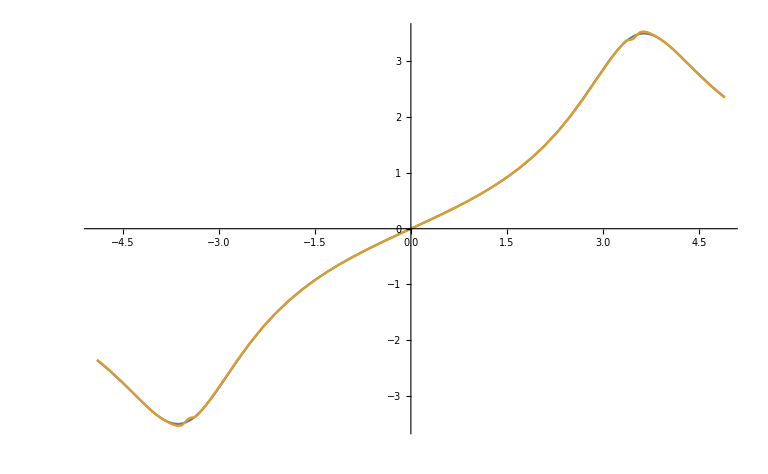

0.00629382

```mathematica
t=3.5;
lim=4.9;
dataEd=Import[outputDir<>"/e_"<>tstr[t]<>".dat"];
eInt=Interpolation[dataEd,InterpolationOrder->3]
Plot[{facT*temp2[t,x,0,{1.2,1}],eInt[x,0,0]^(1/4)},{x,-lim,lim}]
dataux=Import[outputDir<>"/ux_"<>tstr[t]<>".dat"];
uxInt=Interpolation[dataux,InterpolationOrder->3]
Plot[{ux[t,x,0,{1}],uxInt[x,0,0]},{x,-lim,lim}]
Max[Table[Abs[facT*temp2[t,x,0,{1.2,1}]-eInt[x,0,0]^(1/4)],{x,-lim,lim,.01}]]
```

## Compare 3+1d code to Isreal-Stewart Gubser

```mathematica
fpieb=2;
etaS=fpieb/(4Pi);
etaS=0.2;
{Tsol,pisol}={T,pi}/.NDSolve[{T'[p]==-2T[p]/3Tanh[p]-T[p]/3pi[p]Tanh[p],pi'[p]+T[p]pi[p]/(5etaS)-4pi[p]^2Tanh[p]/3==-4Tanh[p]/15,T[0]==1.2,pi[0]==0},{T,pi},{p,-10,10}][[1]];
Tm[t_,r_]:=facT*Tsol[ArcSinh[-(1-t^2+r^2)/2/t]]/t
em[t_,r_]:=Tm[t,r]^4
```

```mathematica
uxExact[t_,x_,y_,{q_}]:=x*Sinh[ArcTanh[2q t q Sqrt[x^2+y^2]/(1+q^2t^2+q^2(x^2+y^2))]]/Sqrt[x^2+y^2]
```

```mathematica
t=1.2;
```

```mathematica
Piso[t_,r_]:=Tm[t,r]^4/3
```

```mathematica
pinnM[t_,r_]:=4Piso[t,r]pisol[ArcSinh[-(1-t^2+r^2)/2/t]]/t^2
```

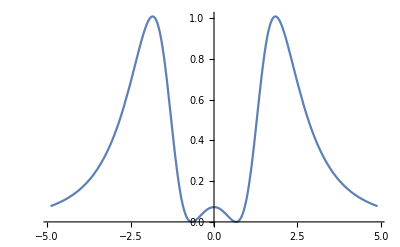

```mathematica
Plot[-t^2pinnM[t,x],{x,-lim,lim}]
```

```mathematica
var[dir_,str_,t_]:=Module[{data,varInt},
data=Import[dir<>"/"<>str<>"_"<>tstr[t]<>".dat"];
Interpolation[data,InterpolationOrder->3]
];
```

```mathematica
Clear[ux]
```

```mathematica
ux=var[outputDir,"ux",t];
uy=var[outputDir,"uy",t];
un=var[outputDir,"un",t];
pixx=var[outputDir,"pixx",t];
pixy=var[outputDir,"pixy",t];
pixn=var[outputDir,"pixn",t];
piyy=var[outputDir,"piyy",t];
piyn=var[outputDir,"piyn",t];
```

```mathematica
pinn[t_,x_,y_,z_]:=Module[{ut,uxs,uys,uns,vx,vy,vn,pixxs,pixys,pixns,piyys,piyns},
uxs=ux[x,y,z];
uys=uy[x,y,z];
uns=un[x,y,z];
ut=Sqrt[1+uxs^2+uys^2+t^2uns^2];
vx=uxs/ut;
vy=uys/ut;
vn=uns/ut;
pixxs=pixx[x,y,z];
pixys=pixy[x,y,z];
pixns=pixn[x,y,z];
piyys=piyy[x,y,z];
piyns=piyn[x,y,z];(pixxs*(vx^2-1)+piyys*(vy^2-1)+2*pixys*vx*vy+2*t^2*(pixns*vx*vn+piyns*vy*vn))/t^2/(1-t^2*vn^2)
]
```

```mathematica
pinn[t,0,0,0]
```

0.0610864

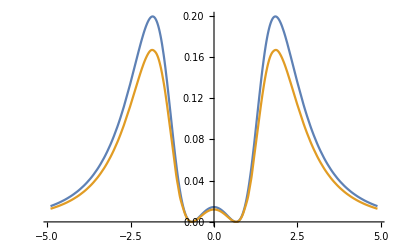

```mathematica
Plot[{-t^2pinnM[t,x]hbarc,pinn[t,x,0,0]hbarc},{x,-lim,lim}]
```

```mathematica
outputDir="/home/bazow/gi/cpu-vh/output";
```

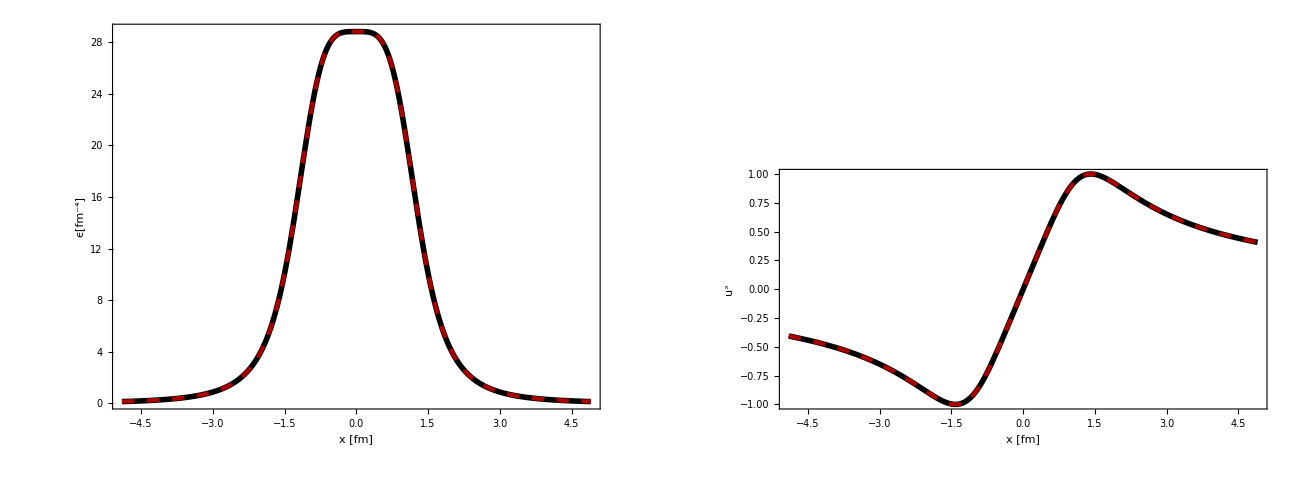

```mathematica
t=1;
lim=4.9;
Off[Interpolation::inhr];
dataEd=Import[outputDir<>"/e_"<>tstr[t]<>".dat"];
eInt=Interpolation[dataEd,InterpolationOrder->3];
dataux=Import[outputDir<>"/ux_"<>tstr[t]<>".dat"];
uxInt=Interpolation[dataux,InterpolationOrder->3];
ePlot=Plot[{em[t,x],eInt[x,0,0]},{x,-lim,lim},PlotRange->All,PlotStyle->{{AbsoluteThickness[4],Darker[Black]},{AbsoluteThickness[3],Dashing[Medium],Darker[Red]}},Frame->True,Axes->False,FrameLabel->{"x [fm]","ϵ[fm^-4]"},FrameStyle->Directive[AbsoluteThickness[1.1]],BaseStyle->{FontFamily->"Times",FontSize->20},ImageSize->600,AspectRatio->0.75,ImagePadding->{{85,30},{80,20}}];
uxPlot=Plot[{uxExact[t,x,0,{1}],uxInt[x,0,0]},{x,-lim,lim},PlotRange->All,PlotStyle->{{AbsoluteThickness[4],Darker[Black]},{AbsoluteThickness[3],Dashing[Medium],Darker[Red]}},Frame->True,Axes->False,FrameLabel->{"x [fm]","u^x"},FrameStyle->Directive[AbsoluteThickness[1.1]],BaseStyle->{FontFamily->"Times",FontSize->20},ImageSize->600,AspectRatio->0.75,Epilog->{Inset[legend,{2,-2.5}],Inset["τ_0="<>ToString[1]<>"fm, τ_f="<>ToString[t]<>" fm",{-2.25,3}],Inset["T_0=1.2 fm^-1, η/𝒮=0.2",{-2.25,2}]},ImagePadding->{{85,30},{80,20}}];
plt=GraphicsGrid[{{ePlot,uxPlot}}]
```

```mathematica
em[t,0]
```

0.0369092

```mathematica
eInt[0,0,0]
```

0.039157

```mathematica
Export["/home/bazow/git/gpu-vh/mathematica/gubserFlowTestPlot.pdf",plt]
```

/home/bazow/git/gpu-vh/mathematica/gubserFlowTestPlot.pdf

```mathematica
16*16*4
```

1024

```mathematica
64*4*4
```

1024

```mathematica
16*16*4
```

1024

```mathematica
32*16
```

512

```mathematica
(*use Documents/cpu/*)
6252.476/65.804
```

95.0167

## 3d visualization

```mathematica
dataEd
```

{{-4.975,-4.975,-0.1,0.0360263},{-4.975,-4.975,-0.05,0.0360263},{-4.975,-4.975,0.,0.0360263},{-4.975,-4.975,0.05,0.0360263},{-4.975,-4.975,0.1,0.0360263},199990,{4.975,4.975,-0.1,0.0360263},{4.975,4.975,-0.05,0.0360263},{4.975,4.975,0.,0.0360263},{4.975,4.975,0.05,0.0360263},{4.975,4.975,0.1,0.0360263}}
 |  |  |  |

```mathematica
eInt[0,0,0]
```

28.8225

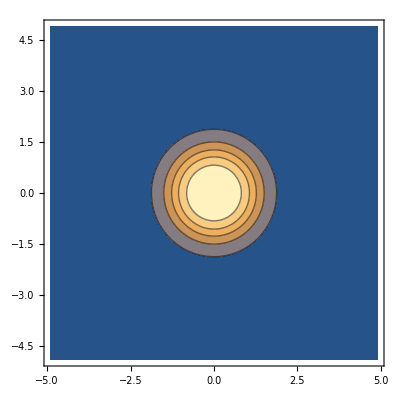

```mathematica
ContourPlot[eInt[x,y,0],{x,-lim,lim},{y,-lim,lim},PlotRange->All]
```

```mathematica
edContour[t_]:=Module[{c1,c2,c3,e1p3,eInt1p3,e1p8,eInt1p8},
e1p3=Import[outputDir1p3<>"/e_"<>tstr[t]<>".dat"];
eInt1p3=Interpolation[e1p3,InterpolationOrder->3];
e1p8=Import[outputDir1p8<>"/e_"<>tstr[t]<>".dat"];
eInt1p8=Interpolation[e1p8,InterpolationOrder->3];
c1=ContourPlot[eInt1p3[x,y,0]^(1/4),{x,-lim,lim},{y,-lim,lim},PlotRange->All];
c2=ContourPlot[eInt1p8[x,y,0]^(1/4),{x,-lim,lim},{y,-lim,lim},PlotRange->All];
c3=ContourPlot[em[t,Sqrt[x^2+y^2]]^(1/4),{x,-lim,lim},{y,-lim,lim},PlotRange->All];
GraphicsGrid[{{c1,c2},{Null,c3}}]
]
```

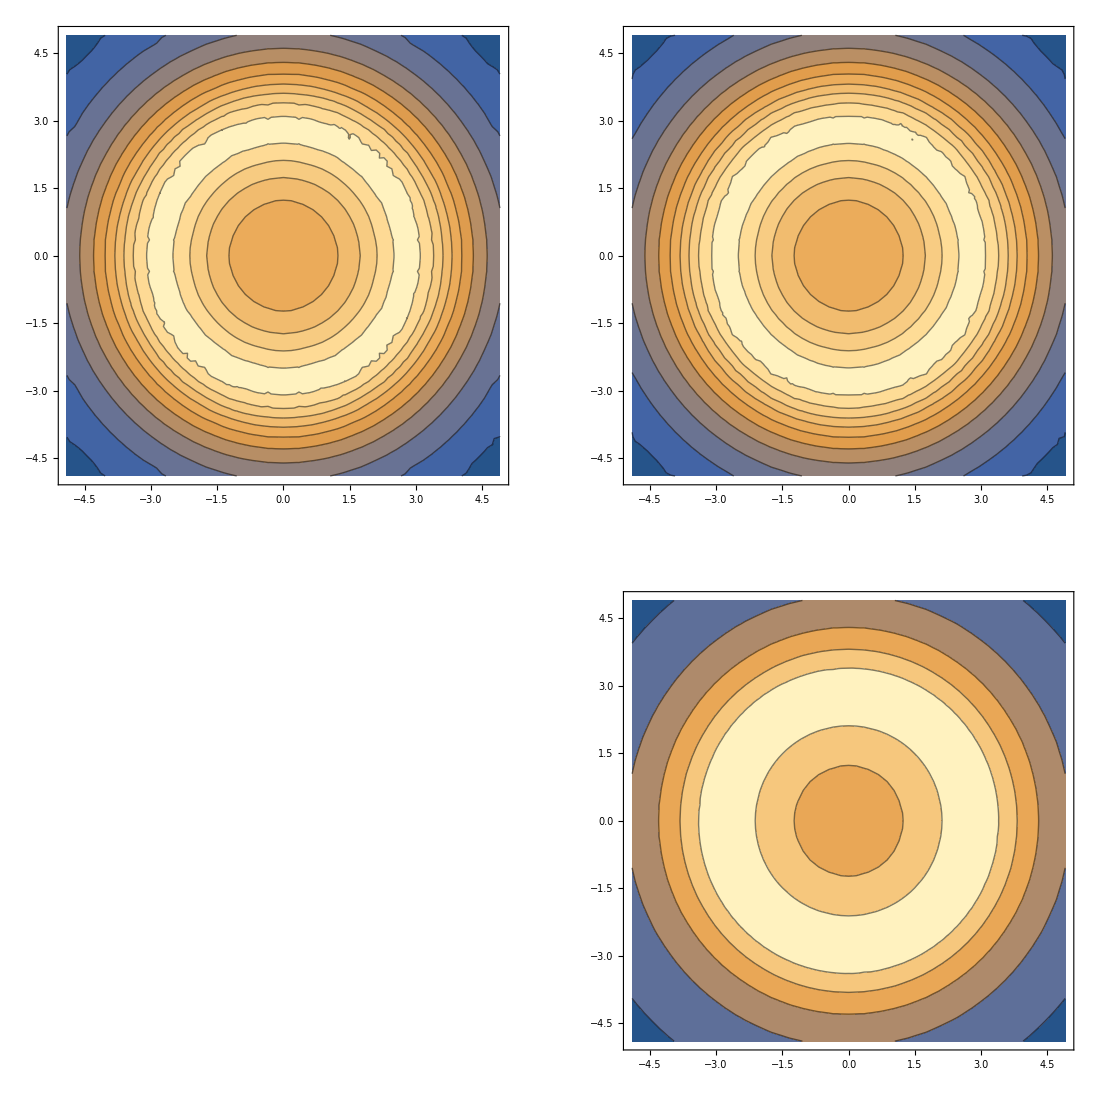

```mathematica
edContour[3]
```

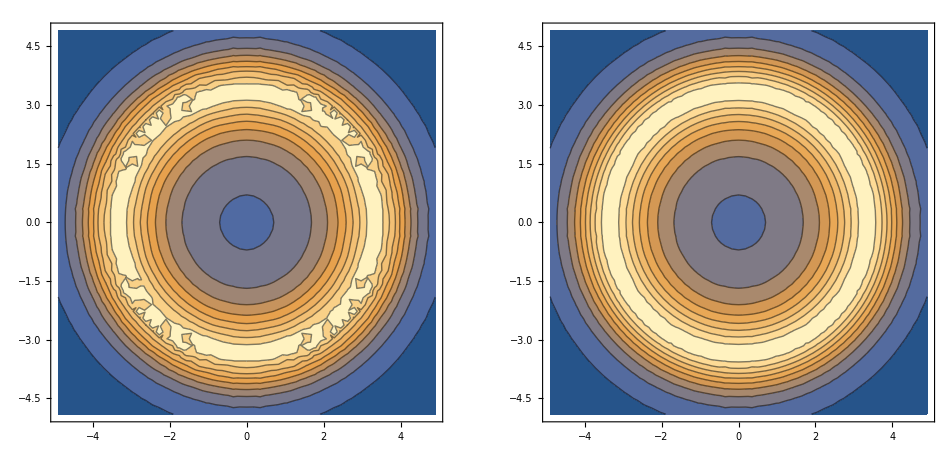

```mathematica
edContour[3.5]
```

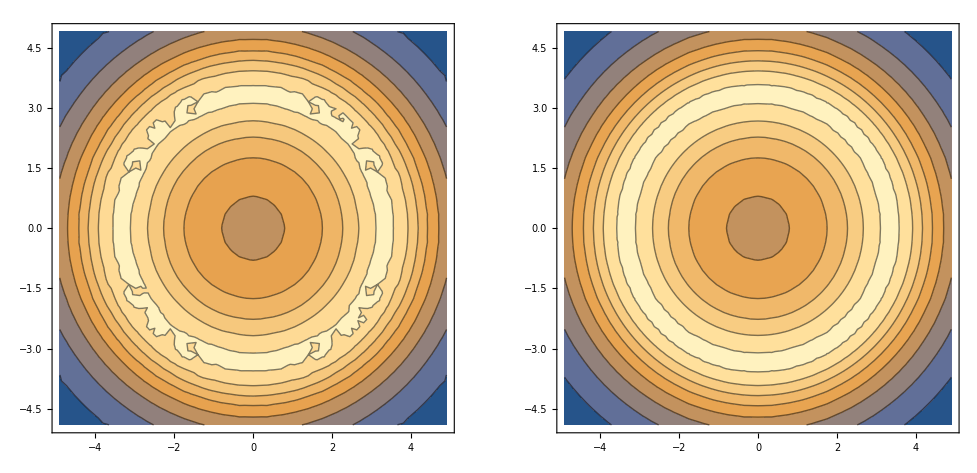

```mathematica
edContour[3.5]
```

```mathematica
data={};
For[i=0,i≤5,i++,
t=1+i*.005;
dataEd=Import[outputDir<>"/e_"<>tstr[t]<>".dat"];
AppendTo[data,dataEd];
]
```